```mathematica
Remove["Global`*"];
(*GSO={{1 ,1, 1, 1,−1, 1, 1 ,1, 1},{1, 1, 1,−1,−1, 1, 1,−1, 1},{1, 1,−1, 1 ,1,−1, 1, 1,−1},{1,−1, 1,−1,−1, 1,−1,−1,−1},{−1,−1, 1,−1, 1 ,1 ,1,−1,−1},{1,−1,−1 ,1, 1, 1, 1,−1, 1},{1,−1, 1,−1 ,1 ,1 ,1,−1,−1},{1,−1, 1,−1,−1,−1,−1, 1,−1},{1 ,1,−1,−1,−1, 1,−1,−1, 1}};*)

GSO={{1, 1, 1,−1, 1, 1 ,1 ,1,−1},{ 1, 1, 1 ,1,−1, 1 ,1, 1,−1},{1, 1,−1,−1, 1,−1, 1,−1, 1},{−1, 1,−1, 1 ,1, 1,−1,−1, 1 },{1,−1 ,1, 1,−1, 1,−1,−1,−1},{1,−1,−1, 1 ,1 ,1 ,1,−1 ,1},{1,−1 ,1,−1,−1, 1, 1,−1,−1},{1 ,1,−1,−1,−1,−1,−1, 1, 1},{−1,−1, 1, 1,−1, 1,−1, 1,−1}};

(*GSO={{1, 1, 1, 1,−1, 1 ,1 ,1,−1},{1, 1 ,1,−1,−1 ,1 ,1, 1,−1 },{1, 1,−1, 1, 1,−1, 1,−1, 1 },{1,−1, 1,−1,−1, 1,−1,−1,−1},{−1,−1, 1,−1, 1 ,1,−1,−1, 1},{1,−1,−1, 1 ,1 ,1, 1, 1,−1},{1,−1, 1,−1,−1, 1 ,1 ,1,−1},{1, 1,−1,−1,−1, 1, 1, 1,−1},{−1,−1, 1,−1, 1,−1,−1,−1,−1}};*)



S={{1,1,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1}};
GGSO=Table[Boole[GSO[[i,j]]==-1],{i,1,9},{j,1,9}];

Z=ϑ[a,b]*ϑ[a+h2,b+g2]*ϑ[a+h1,b+g1]*ϑ[a-h1-h2,b-g1-g2]*ϑ̄[k+h1,l+g1]*ϑ̄[k+h2,l+g2]*ϑ̄[k,l]*(ϑ̄[k-h1-h2,l-g1-g2])^5*(ϑ̄[ρ,σ])^4*(ϑ̄[ρ+H,σ+G])^4;
χ=(a+k)*(g1+g2+g1*g2)+(b+l)*(h1*g2+h2*g1);


ModularS={ϑ[a_,b_]->(-1)^(a*b/2),ϑ̄[a_,b_]->(-1)^(-a*b/2)};
ModularT={ϑ[a_,b_]->(-1)^(-a/4),ϑ̄[a_,b_]->(-1)^(a/4)};
SFactor=(Exponent[Z/.ModularS,-1]//FullSimplify)//.{a_*b_/;Mod[a,2]==0->0*b};
TFactor=(1+Exponent[Z/.ModularT,-1]//FullSimplify)//.{a_*b_ /;Mod[a,2]==0->0*b};

(*Print[SFactor];
Print[TFactor];*)

Ω=Array[ω,{9,9}];
Γ={a,k,ρ,h1,h2,H1,H2,H3,H};
Δ={b,l,σ,g1,g2,G1,G2,G3,G};
SΓ={b,l,σ,g1,g2,G1,G2,G3,G};
SΔ={-a,-k,-ρ,-h1,-h2,-H1,-H2,-H3,-H};
TΓ={a,k,ρ,h1,h2,H1,H2,H3,H};
TΔ={a+b-1,k+l-1,ρ+σ-1,h1+g1,h2+g2,H1+G1-1,H2+G2-1,H3+G3-1,H+G};
Φ=ExpandAll[Γ.Ω.Δ];
Ψ = a+b+Φ;
SΦ=ExpandAll[SΓ.Ω.SΔ+SFactor]/.{d_^2->d};
SΨ=a+b+SΦ;
TΦ=ExpandAll[TΓ.Ω.TΔ+TFactor]/.{d_^2->d};
TΨ=b-1+TΦ;

TEQ0 = TΨ/.Thread[Γ->0]/.Thread[Δ->0];
SEQ0 = SΨ/.Thread[Γ->0]/.Thread[Δ->0];
TEQ1A=Table[Coefficient[TΨ,Γ[[i]]]/.Thread[Γ->0]/.Thread[Δ->0],{i,1,9}];
TEQ1B=Table[Coefficient[TΨ,Δ[[i]]]/.Thread[Γ->0]/.Thread[Δ->0],{i,1,9}];
SEQ1A=Table[Coefficient[SΨ,Γ[[i]]]/.Thread[Γ->0]/.Thread[Δ->0],{i,1,9}];
SEQ1B=Table[Coefficient[SΨ,Δ[[i]]]/.Thread[Γ->0]/.Thread[Δ->0],{i,1,9}];
TEQ2=Table[Coefficient[TΨ,Γ[[i]]*Δ[[j]]],{i,1,9},{j,1,9}]//.{a_*d_/;Mod[a,2]==0->0*d};
SEQ2=Table[Coefficient[SΨ,Γ[[i]]*Δ[[j]]],{i,1,9},{j,1,9}]//.{a_*d_/;Mod[a,2]==0->0*d,-d_->d};
EQ0 = 0;
EQ1A = Table[Coefficient[Ψ,Γ[[i]]]/.Thread[Γ->0]/.Thread[Δ->0],{i,1,9}];
EQ1B = Table[Coefficient[Ψ,Δ[[i]]]/.Thread[Γ->0]/.Thread[Δ->0],{i,1,9}];
EQ2 = Ω;

(*SimplifyNotation=Flatten[Table[ω[i,j]->Subscript[ω, ToString[i]<>ToString[j]],{i,1,9},{j,1,9}]];
Print["O^th order: ", EQ0//MatrixForm," = ",SEQ0//MatrixForm];
Print["1^th order (Γ): ", EQ1A//MatrixForm," = ",SEQ1A/.SimplifyNotation//MatrixForm];
Print["1^th order (Δ): ", EQ1B//MatrixForm," = ",SEQ1B/.SimplifyNotation//MatrixForm];
Print["2^th order (Ω): ", EQ2/.SimplifyNotation//MatrixForm," = ",SEQ2/.SimplifyNotation//MatrixForm];
SimplifyNotation=Flatten[Table[ω[i,j]->Subscript[ω, ToString[i]<>ToString[j]],{i,1,9},{j,1,9}]];
Print["O^th order: ", EQ0//MatrixForm," = ",TEQ0//MatrixForm];
Print["1^th order (Γ): ", EQ1A//MatrixForm," = ",TEQ1A/.SimplifyNotation//MatrixForm];
Print["1^th order (Δ): ", EQ1B//MatrixForm," = ",TEQ1B/.SimplifyNotation//MatrixForm];
Print["2^th order (Ω): ", EQ2/.SimplifyNotation//MatrixForm," = ",TEQ2/.SimplifyNotation//MatrixForm];*)

SImplement=Flatten[Solve[EQ2==SEQ2]];
TImplement={ω[1,2]->ω[1,3]+ω[1,6]+ω[1,7]+ω[1,8],
ω[1,2]->ω[2,3]+ω[2,6]+ω[2,7]+ω[2,8],
ω[1,3]->ω[2,3]+ω[3,6]+ω[3,7]+ω[3,8],
ω[1,4]->ω[2,4]+ω[3,4]+ω[4,4]+ω[4,6]+ω[4,7]+ω[4,8]+1,
ω[1,5]->ω[2,5]+ω[3,5]+ω[5,5]+ω[5,6]+ω[5,7]+ω[5,8]+1,
ω[1,6]->ω[2,6]+ω[3,6]+ω[6,7]+ω[6,8],
ω[1,7]->ω[2,7]+ω[3,7]+ω[6,7]+ω[7,8],
ω[1,8]->ω[2,8]+ω[3,8]+ω[6,8]+ω[7,8],
ω[1,9]->ω[2,9]+ω[3,9]+ω[6,9]+ω[7,9]+ω[8,9]+ω[9,9]+1};

P=Mod[Table[a+b+χ/.Thread[Γ->S[[i,;;]]]/.Thread[Δ->S[[j,;;]]],{i,1,9},{j,1,9}],2];
Ω̃=S.Ω.Transpose[S];
TransEq = Thread[Flatten[GGSO+P]==Flatten[Ω̃]];
TransSol=Flatten[Solve[TransEq]];
ΦSol =Γ.(Mod[Ω/.TransSol,2]).Δ ;
ΨSol = a+b+ΦSol;
Print[ΨSol];
```

a+b+G3 (H+h2+H3+k)+g2 (H+H2+H3+k)+g1 (H1+ρ)+G2 (a+H1+h2+ρ)+b (H1+H2+k+ρ)+G1 (a+h1+H1+H2+k+ρ)+G (H+h2+H3+k+ρ)+l (a+H+H1+h2+H3+k+ρ)+(a+H+h1+H1+H2+k+ρ) σ

```mathematica
Remove["Global`*"];
ΨSol =a+b+G3 (H+h2+H3+k)+g2 (H+H2+H3+k)+g1 (H1+ρ)+G2 (a+H1+h2+ρ)+b (H1+H2+k+ρ)+G1 (a+h1+H1+H2+k+ρ)+G (H+h2+H3+k+ρ)+l (a+H+H1+h2+H3+k+ρ)+(a+H+h1+H1+H2+k+ρ) σ;
χ=(a+k)*(g1+g2+g1*g2)+(b+l)*(h1*g2+h2*g1);
X={};
Y={};
For[in=1,in<=24,in++,

T1=0;U1=0;U2=1;
T2=in/12;
T=T1+I*T2;
U=U1+I*U2;

j=8;

PL=1/(√(2*T2*U2))*((U1+I*U2)/2*(m1+n1-k)-1/2*(m2+n2-k)+(T1+I*T2)*(m1-n1+H1)+(T1+I*T2)*(U1+I*U2)*(m2-n2+H1));
PR=1/(√(2*T2*U2))*((U1+I*U2)/2*(m1+n1-k)-1/2*(m2+n2-k)+(T1-I*T2)*(m1-n1+H1)-(T1+I*T2)*(U1+I*U2)*(m2-n2+H1));
PLC=1/(√(2*T2*U2))*((U1-I*U2)/2*(m1+n1-k)-1/2*(m2+n2-k)+(T1-I*T2)*(m1-n1+H1)+(T1-I*T2)*(U1-I*U2)*(m2-n2+H1));
PRC=1/(√(2*T2*U2))*((U1-I*U2)/2*(m1+n1-k)-1/2*(m2+n2-k)+(T1+I*T2)*(m1-n1+H1)-(T1-I*T2)*(U1-I*U2)*(m2-n2+H1));



f11=Normal[Series[Sum[(p^(1-m1^2/2-m2^2/2-n1+n1^2/2-n2+n2^2/2+1/(4 T2)-m1/(4 T2)+m1^2/(8 T2)-m2/(4 T2)+m2^2/(8 T2)-n1/(4 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)-n2/(4 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+T2+m1 T2+(m1^2 T2)/2+m2 T2+(m2^2 T2)/2-n1 T2-m1 n1 T2+(n1^2 T2)/2-n2 T2-m2 n2 T2+(n2^2 T2)/2) q^(-1+m1^2/2+m2^2/2+n1-n1^2/2+n2-n2^2/2+1/(4 T2)-m1/(4 T2)+m1^2/(8 T2)-m2/(4 T2)+m2^2/(8 T2)-n1/(4 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)-n2/(4 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+T2+m1 T2+(m1^2 T2)/2+m2 T2+(m2^2 T2)/2-n1 T2-m1 n1 T2+(n1^2 T2)/2-n2 T2-m2 n2 T2+(n2^2 T2)/2)),{n1,-j,j},{m1,-j,j},{n2,-j,j},{m2,-j,j}],{q,0,4},{p,0,4}]];
f12=Normal[Series[Sum[(p^(-m1/2-m1^2/2-m2/2-m2^2/2-n1/2+n1^2/2-n2/2+n2^2/2+m1^2/(8 T2)+m2^2/(8 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+T2+m1 T2+(m1^2 T2)/2+m2 T2+(m2^2 T2)/2-n1 T2-m1 n1 T2+(n1^2 T2)/2-n2 T2-m2 n2 T2+(n2^2 T2)/2) q^(m1/2+m1^2/2+m2/2+m2^2/2+n1/2-n1^2/2+n2/2-n2^2/2+m1^2/(8 T2)+m2^2/(8 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+T2+m1 T2+(m1^2 T2)/2+m2 T2+(m2^2 T2)/2-n1 T2-m1 n1 T2+(n1^2 T2)/2-n2 T2-m2 n2 T2+(n2^2 T2)/2)),{n1,-j,j},{m1,-j,j},{n2,-j,j},{m2,-j,j}],{q,0,4},{p,0,4}]];
f13=Normal[Series[Sum[(p^(m1/2-m1^2/2+m2/2-m2^2/2-n1/2+n1^2/2-n2/2+n2^2/2+1/(4 T2)-m1/(4 T2)+m1^2/(8 T2)-m2/(4 T2)+m2^2/(8 T2)-n1/(4 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)-n2/(4 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+(m1^2 T2)/2+(m2^2 T2)/2-m1 n1 T2+(n1^2 T2)/2-m2 n2 T2+(n2^2 T2)/2) q^(-m1/2+m1^2/2-m2/2+m2^2/2+n1/2-n1^2/2+n2/2-n2^2/2+1/(4 T2)-m1/(4 T2)+m1^2/(8 T2)-m2/(4 T2)+m2^2/(8 T2)-n1/(4 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)-n2/(4 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+(m1^2 T2)/2+(m2^2 T2)/2-m1 n1 T2+(n1^2 T2)/2-m2 n2 T2+(n2^2 T2)/2)),{n1,-j,j},{m1,-j,j},{n2,-j,j},{m2,-j,j}],{q,0,4},{p,0,4}]];
f14=Normal[Series[Sum[(p^(-m1^2/2-m2^2/2+n1^2/2+n2^2/2+m1^2/(8 T2)+m2^2/(8 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+(m1^2 T2)/2+(m2^2 T2)/2-m1 n1 T2+(n1^2 T2)/2-m2 n2 T2+(n2^2 T2)/2) q^(m1^2/2+m2^2/2-n1^2/2-n2^2/2+m1^2/(8 T2)+m2^2/(8 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+(m1^2 T2)/2+(m2^2 T2)/2-m1 n1 T2+(n1^2 T2)/2-m2 n2 T2+(n2^2 T2)/2)),{n1,-j,j},{m1,-j,j},{n2,-j,j},{m2,-j,j}],{q,0,4},{p,0,4}]];



f21=Normal[Series[Sum[(-1)^(m1+n1+m2+n2)*(p^(1-m1^2/2-m2^2/2-n1+n1^2/2-n2+n2^2/2+1/(4 T2)-m1/(4 T2)+m1^2/(8 T2)-m2/(4 T2)+m2^2/(8 T2)-n1/(4 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)-n2/(4 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+T2+m1 T2+(m1^2 T2)/2+m2 T2+(m2^2 T2)/2-n1 T2-m1 n1 T2+(n1^2 T2)/2-n2 T2-m2 n2 T2+(n2^2 T2)/2) q^(-1+m1^2/2+m2^2/2+n1-n1^2/2+n2-n2^2/2+1/(4 T2)-m1/(4 T2)+m1^2/(8 T2)-m2/(4 T2)+m2^2/(8 T2)-n1/(4 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)-n2/(4 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+T2+m1 T2+(m1^2 T2)/2+m2 T2+(m2^2 T2)/2-n1 T2-m1 n1 T2+(n1^2 T2)/2-n2 T2-m2 n2 T2+(n2^2 T2)/2)),{n1,-j,j},{m1,-j,j},{n2,-j,j},{m2,-j,j}],{q,0,4},{p,0,4}]];
f22=Normal[Series[Sum[(-1)^(m1+n1+m2+n2)*(p^(-m1/2-m1^2/2-m2/2-m2^2/2-n1/2+n1^2/2-n2/2+n2^2/2+m1^2/(8 T2)+m2^2/(8 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+T2+m1 T2+(m1^2 T2)/2+m2 T2+(m2^2 T2)/2-n1 T2-m1 n1 T2+(n1^2 T2)/2-n2 T2-m2 n2 T2+(n2^2 T2)/2) q^(m1/2+m1^2/2+m2/2+m2^2/2+n1/2-n1^2/2+n2/2-n2^2/2+m1^2/(8 T2)+m2^2/(8 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+T2+m1 T2+(m1^2 T2)/2+m2 T2+(m2^2 T2)/2-n1 T2-m1 n1 T2+(n1^2 T2)/2-n2 T2-m2 n2 T2+(n2^2 T2)/2)),{n1,-j,j},{m1,-j,j},{n2,-j,j},{m2,-j,j}],{q,0,4},{p,0,4}]];
f23=Normal[Series[Sum[(-1)^(m1+n1+m2+n2)*(p^(m1/2-m1^2/2+m2/2-m2^2/2-n1/2+n1^2/2-n2/2+n2^2/2+1/(4 T2)-m1/(4 T2)+m1^2/(8 T2)-m2/(4 T2)+m2^2/(8 T2)-n1/(4 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)-n2/(4 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+(m1^2 T2)/2+(m2^2 T2)/2-m1 n1 T2+(n1^2 T2)/2-m2 n2 T2+(n2^2 T2)/2) q^(-m1/2+m1^2/2-m2/2+m2^2/2+n1/2-n1^2/2+n2/2-n2^2/2+1/(4 T2)-m1/(4 T2)+m1^2/(8 T2)-m2/(4 T2)+m2^2/(8 T2)-n1/(4 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)-n2/(4 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+(m1^2 T2)/2+(m2^2 T2)/2-m1 n1 T2+(n1^2 T2)/2-m2 n2 T2+(n2^2 T2)/2)),{n1,-j,j},{m1,-j,j},{n2,-j,j},{m2,-j,j}],{q,0,4},{p,0,4}]];
f24=Normal[Series[Sum[(-1)^(m1+n1+m2+n2)*(p^(-m1^2/2-m2^2/2+n1^2/2+n2^2/2+m1^2/(8 T2)+m2^2/(8 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+(m1^2 T2)/2+(m2^2 T2)/2-m1 n1 T2+(n1^2 T2)/2-m2 n2 T2+(n2^2 T2)/2) q^(m1^2/2+m2^2/2-n1^2/2-n2^2/2+m1^2/(8 T2)+m2^2/(8 T2)+(m1 n1)/(4 T2)+n1^2/(8 T2)+(m2 n2)/(4 T2)+n2^2/(8 T2)+(m1^2 T2)/2+(m2^2 T2)/2-m1 n1 T2+(n1^2 T2)/2-m2 n2 T2+(n2^2 T2)/2)),{n1,-j,j},{m1,-j,j},{n2,-j,j},{m2,-j,j}],{q,0,4},{p,0,4}]];


f=If[Mod[G1+l,2]==0,
If[k==1&&H1==1,f11,If[k==0&&H1==1,f12,If[k==1&&H1==0,f13,f14]]],
If[k==1&&H1==1,f21,If[k==0&&H1==1,f22,If[k==1&&H1==0,f23,f24]]]];

(*f=Normal[Series[Sum[(-1)^((m1+n1+m2+n2)*(G1+l))*(q^(-H1 k+(H1 m1)/2-(k m1)/2+m1^2/2+(H1 m2)/2-(k m2)/2+m2^2/2+(H1 n1)/2+(k n1)/2-n1^2/2+(H1 n2)/2+(k n2)/2-n2^2/2+k^2/(8 T2 U2)-(k m2)/(4 T2 U2)+m2^2/(8 T2 U2)-(k n2)/(4 T2 U2)+(m2 n2)/(4 T2 U2)+n2^2/(8 T2 U2)+(H1 k T1)/(2 T2 U2)+(k m1 T1)/(2 T2 U2)-(H1 m2 T1)/(2 T2 U2)-(m1 m2 T1)/(2 T2 U2)-(k n1 T1)/(2 T2 U2)+(m2 n1 T1)/(2 T2 U2)-(H1 n2 T1)/(2 T2 U2)-(m1 n2 T1)/(2 T2 U2)+(n1 n2 T1)/(2 T2 U2)+(H1^2 T1^2)/(2 T2 U2)+(H1 m1 T1^2)/(T2 U2)+(m1^2 T1^2)/(2 T2 U2)-(H1 n1 T1^2)/(T2 U2)-(m1 n1 T1^2)/(T2 U2)+(n1^2 T1^2)/(2 T2 U2)+(H1^2 T2)/(2 U2)+(H1 m1 T2)/U2+(m1^2 T2)/(2 U2)-(H1 n1 T2)/U2-(m1 n1 T2)/U2+(n1^2 T2)/(2 U2)-(k^2 U1)/(4 T2 U2)+(k m1 U1)/(4 T2 U2)+(k m2 U1)/(4 T2 U2)-(m1 m2 U1)/(4 T2 U2)+(k n1 U1)/(4 T2 U2)-(m2 n1 U1)/(4 T2 U2)+(k n2 U1)/(4 T2 U2)-(m1 n2 U1)/(4 T2 U2)-(n1 n2 U1)/(4 T2 U2)+(H1 m1 T1 U1)/(2 T2 U2)-(k m1 T1 U1)/(2 T2 U2)+(m1^2 T1 U1)/(2 T2 U2)-(H1 m2 T1 U1)/(2 T2 U2)+(k m2 T1 U1)/(2 T2 U2)-(m2^2 T1 U1)/(2 T2 U2)+(H1 n1 T1 U1)/(2 T2 U2)+(k n1 T1 U1)/(2 T2 U2)-(n1^2 T1 U1)/(2 T2 U2)-(H1 n2 T1 U1)/(2 T2 U2)-(k n2 T1 U1)/(2 T2 U2)+(n2^2 T1 U1)/(2 T2 U2)+(H1^2 T1^2 U1)/(T2 U2)+(H1 m1 T1^2 U1)/(T2 U2)+(H1 m2 T1^2 U1)/(T2 U2)+(m1 m2 T1^2 U1)/(T2 U2)-(H1 n1 T1^2 U1)/(T2 U2)-(m2 n1 T1^2 U1)/(T2 U2)-(H1 n2 T1^2 U1)/(T2 U2)-(m1 n2 T1^2 U1)/(T2 U2)+(n1 n2 T1^2 U1)/(T2 U2)+(H1^2 T2 U1)/U2+(H1 m1 T2 U1)/U2+(H1 m2 T2 U1)/U2+(m1 m2 T2 U1)/U2-(H1 n1 T2 U1)/U2-(m2 n1 T2 U1)/U2-(H1 n2 T2 U1)/U2-(m1 n2 T2 U1)/U2+(n1 n2 T2 U1)/U2+(k^2 U1^2)/(8 T2 U2)-(k m1 U1^2)/(4 T2 U2)+(m1^2 U1^2)/(8 T2 U2)-(k n1 U1^2)/(4 T2 U2)+(m1 n1 U1^2)/(4 T2 U2)+(n1^2 U1^2)/(8 T2 U2)-(H1 k T1 U1^2)/(2 T2 U2)+(H1 m1 T1 U1^2)/(2 T2 U2)-(k m2 T1 U1^2)/(2 T2 U2)+(m1 m2 T1 U1^2)/(2 T2 U2)+(H1 n1 T1 U1^2)/(2 T2 U2)+(m2 n1 T1 U1^2)/(2 T2 U2)+(k n2 T1 U1^2)/(2 T2 U2)-(m1 n2 T1 U1^2)/(2 T2 U2)-(n1 n2 T1 U1^2)/(2 T2 U2)+(H1^2 T1^2 U1^2)/(2 T2 U2)+(H1 m2 T1^2 U1^2)/(T2 U2)+(m2^2 T1^2 U1^2)/(2 T2 U2)-(H1 n2 T1^2 U1^2)/(T2 U2)-(m2 n2 T1^2 U1^2)/(T2 U2)+(n2^2 T1^2 U1^2)/(2 T2 U2)+(H1^2 T2 U1^2)/(2 U2)+(H1 m2 T2 U1^2)/U2+(m2^2 T2 U1^2)/(2 U2)-(H1 n2 T2 U1^2)/U2-(m2 n2 T2 U1^2)/U2+(n2^2 T2 U1^2)/(2 U2)+(k^2 U2)/(8 T2)-(k m1 U2)/(4 T2)+(m1^2 U2)/(8 T2)-(k n1 U2)/(4 T2)+(m1 n1 U2)/(4 T2)+(n1^2 U2)/(8 T2)-(H1 k T1 U2)/(2 T2)+(H1 m1 T1 U2)/(2 T2)-(k m2 T1 U2)/(2 T2)+(m1 m2 T1 U2)/(2 T2)+(H1 n1 T1 U2)/(2 T2)+(m2 n1 T1 U2)/(2 T2)+(k n2 T1 U2)/(2 T2)-(m1 n2 T1 U2)/(2 T2)-(n1 n2 T1 U2)/(2 T2)+(H1^2 T1^2 U2)/(2 T2)+(H1 m2 T1^2 U2)/T2+(m2^2 T1^2 U2)/(2 T2)-(H1 n2 T1^2 U2)/T2-(m2 n2 T1^2 U2)/T2+(n2^2 T1^2 U2)/(2 T2)+1/2 H1^2 T2 U2+H1 m2 T2 U2+1/2 m2^2 T2 U2-H1 n2 T2 U2-m2 n2 T2 U2+1/2 n2^2 T2 U2)p^(H1 k-(H1 m1)/2+(k m1)/2-m1^2/2-(H1 m2)/2+(k m2)/2-m2^2/2-(H1 n1)/2-(k n1)/2+n1^2/2-(H1 n2)/2-(k n2)/2+n2^2/2+2 H1^2 T1+2 H1 m1 T1+2 H1 m2 T1+2 m1 m2 T1-2 H1 n1 T1-2 m2 n1 T1-2 H1 n2 T1-2 m1 n2 T1+2 n1 n2 T1+k^2/(8 T2 U2)-(k m2)/(4 T2 U2)+m2^2/(8 T2 U2)-(k n2)/(4 T2 U2)+(m2 n2)/(4 T2 U2)+n2^2/(8 T2 U2)+(H1 k T1)/(2 T2 U2)+(k m1 T1)/(2 T2 U2)-(H1 m2 T1)/(2 T2 U2)-(m1 m2 T1)/(2 T2 U2)-(k n1 T1)/(2 T2 U2)+(m2 n1 T1)/(2 T2 U2)-(H1 n2 T1)/(2 T2 U2)-(m1 n2 T1)/(2 T2 U2)+(n1 n2 T1)/(2 T2 U2)+(H1^2 T1^2)/(2 T2 U2)+(H1 m1 T1^2)/(T2 U2)+(m1^2 T1^2)/(2 T2 U2)-(H1 n1 T1^2)/(T2 U2)-(m1 n1 T1^2)/(T2 U2)+(n1^2 T1^2)/(2 T2 U2)+(H1^2 T2)/(2 U2)+(H1 m1 T2)/U2+(m1^2 T2)/(2 U2)-(H1 n1 T2)/U2-(m1 n1 T2)/U2+(n1^2 T2)/(2 U2)-(k^2 U1)/(4 T2 U2)+(k m1 U1)/(4 T2 U2)+(k m2 U1)/(4 T2 U2)-(m1 m2 U1)/(4 T2 U2)+(k n1 U1)/(4 T2 U2)-(m2 n1 U1)/(4 T2 U2)+(k n2 U1)/(4 T2 U2)-(m1 n2 U1)/(4 T2 U2)-(n1 n2 U1)/(4 T2 U2)-(H1 k T1 U1)/(T2 U2)+(H1 m1 T1 U1)/(2 T2 U2)-(k m1 T1 U1)/(2 T2 U2)+(m1^2 T1 U1)/(2 T2 U2)+(H1 m2 T1 U1)/(2 T2 U2)-(k m2 T1 U1)/(2 T2 U2)+(m2^2 T1 U1)/(2 T2 U2)+(H1 n1 T1 U1)/(2 T2 U2)+(k n1 T1 U1)/(2 T2 U2)-(n1^2 T1 U1)/(2 T2 U2)+(H1 n2 T1 U1)/(2 T2 U2)+(k n2 T1 U1)/(2 T2 U2)-(n2^2 T1 U1)/(2 T2 U2)-(H1^2 T1^2 U1)/(T2 U2)-(H1 m1 T1^2 U1)/(T2 U2)-(H1 m2 T1^2 U1)/(T2 U2)-(m1 m2 T1^2 U1)/(T2 U2)+(H1 n1 T1^2 U1)/(T2 U2)+(m2 n1 T1^2 U1)/(T2 U2)+(H1 n2 T1^2 U1)/(T2 U2)+(m1 n2 T1^2 U1)/(T2 U2)-(n1 n2 T1^2 U1)/(T2 U2)+(H1^2 T2 U1)/U2+(H1 m1 T2 U1)/U2+(H1 m2 T2 U1)/U2+(m1 m2 T2 U1)/U2-(H1 n1 T2 U1)/U2-(m2 n1 T2 U1)/U2-(H1 n2 T2 U1)/U2-(m1 n2 T2 U1)/U2+(n1 n2 T2 U1)/U2+(k^2 U1^2)/(8 T2 U2)-(k m1 U1^2)/(4 T2 U2)+(m1^2 U1^2)/(8 T2 U2)-(k n1 U1^2)/(4 T2 U2)+(m1 n1 U1^2)/(4 T2 U2)+(n1^2 U1^2)/(8 T2 U2)+(H1 k T1 U1^2)/(2 T2 U2)-(H1 m1 T1 U1^2)/(2 T2 U2)+(k m2 T1 U1^2)/(2 T2 U2)-(m1 m2 T1 U1^2)/(2 T2 U2)-(H1 n1 T1 U1^2)/(2 T2 U2)-(m2 n1 T1 U1^2)/(2 T2 U2)-(k n2 T1 U1^2)/(2 T2 U2)+(m1 n2 T1 U1^2)/(2 T2 U2)+(n1 n2 T1 U1^2)/(2 T2 U2)+(H1^2 T1^2 U1^2)/(2 T2 U2)+(H1 m2 T1^2 U1^2)/(T2 U2)+(m2^2 T1^2 U1^2)/(2 T2 U2)-(H1 n2 T1^2 U1^2)/(T2 U2)-(m2 n2 T1^2 U1^2)/(T2 U2)+(n2^2 T1^2 U1^2)/(2 T2 U2)+(H1^2 T2 U1^2)/(2 U2)+(H1 m2 T2 U1^2)/U2+(m2^2 T2 U1^2)/(2 U2)-(H1 n2 T2 U1^2)/U2-(m2 n2 T2 U1^2)/U2+(n2^2 T2 U1^2)/(2 U2)+(k^2 U2)/(8 T2)-(k m1 U2)/(4 T2)+(m1^2 U2)/(8 T2)-(k n1 U2)/(4 T2)+(m1 n1 U2)/(4 T2)+(n1^2 U2)/(8 T2)+(H1 k T1 U2)/(2 T2)-(H1 m1 T1 U2)/(2 T2)+(k m2 T1 U2)/(2 T2)-(m1 m2 T1 U2)/(2 T2)-(H1 n1 T1 U2)/(2 T2)-(m2 n1 T1 U2)/(2 T2)-(k n2 T1 U2)/(2 T2)+(m1 n2 T1 U2)/(2 T2)+(n1 n2 T1 U2)/(2 T2)+(H1^2 T1^2 U2)/(2 T2)+(H1 m2 T1^2 U2)/T2+(m2^2 T1^2 U2)/(2 T2)-(H1 n2 T1^2 U2)/T2-(m2 n2 T1^2 U2)/T2+(n2^2 T1^2 U2)/(2 T2)+1/2 H1^2 T2 U2+H1 m2 T2 U2+1/2 m2^2 T2 U2-H1 n2 T2 U2-m2 n2 T2 U2+1/2 n2^2 T2 U2)),{n1,-j,j},{m1,-j,j},{n2,-j,j},{m2,-j,j}],{q,0,2},{p,0,2}]];*)



ΓR=If[h2==0&&g2==0,f,ϑ[k+H1,l+G1]*ϑ[k+H1+h2,l+G1+g2]*ϑ̄[k+H1,l+G1]*ϑ̄[k+H1+h2,l+G1+g2]];

ΓLattice=ϑ[k+H2,l+G2]*ϑ[k+H2+h1,l+G2+g1]*ϑ[k+H3,l+G3]*ϑ[k+H3-h1-h2,l+G3-g1-g2]*
ϑ̄[k+H2,l+G2]*ϑ̄[k+H2+h1,l+G2+g1]*ϑ̄[k+H3,l+G3]*ϑ̄[k+H3-h1-h2,l+G3-g1-g2]*ΓR;
Z=ϑ[a,b]*ϑ[a+h2,b+g2]*ϑ[a+h1,b+g1]*ϑ[a-h1-h2,b-g1-g2]*ϑ̄[k+h1,l+g1]*ϑ̄[k+h2,l+g2]*ϑ̄[k,l]*(ϑ̄[k-h1-h2,l-g1-g2])^5*(ϑ̄[ρ,σ])^4*(ϑ̄[ρ+H,σ+G])^4*ΓLattice;



Zq=
1/2^9*1/(η^12*(η̄)^24)*Sum[If[Mod[a,2]+Mod[b,2]==2||Mod[a+h1,2]+Mod[b+g1,2]==2||Mod[a+h2,2]+Mod[b+g2,2]==2||Mod[a-h1-h2,2]+Mod[b-g1-g2,2]==2||Mod[k,2]+Mod[l,2]==2||Mod[k+h1,2]+Mod[l+g1,2]==2||Mod[k+h2,2]+Mod[l+g2,2]==2||Mod[k-h1-h2,2]+Mod[l-g1-g2,2]==2||Mod[ρ,2]+Mod[σ,2]==2||Mod[ρ+H,2]+Mod[σ+G,2]==2,0,
(-1)^(ΨSol+χ)*Z],{a,0,1},{k,0,1},{ρ,0,1},{b,0,1},{l,0,1},{σ,0,1},{H1,0,1},{H2,0,1},{H3,0,1},{H,0,1},{h1,0,1},{h2,0,1},{G1,0,1},{G2,0,1},{G3,0,1},{G,0,1},{g1,0,1},{g2,0,1}];

ϑ[a_,b_]:=If[Mod[a,2]==0&&Mod[b,2]==0,EllipticTheta[3,q],If[Mod[a,2]==0&&Mod[b,2]==1,EllipticTheta[4,q],If[Mod[a,2]==1&&Mod[b,2]==0,EllipticTheta[2,q],If[Mod[a,2]==1&&Mod[b,2]==1,0,]]]];
ϑ̄[a_,b_]:=If[Mod[a,2]==0&&Mod[b,2]==0,EllipticTheta[3,p],If[Mod[a,2]==0&&Mod[b,2]==1,EllipticTheta[4,p],If[Mod[a,2]==1&&Mod[b,2]==0,EllipticTheta[2,p],If[Mod[a,2]==1&&Mod[b,2]==1,0,]]]];
η=q^(2/24)*QPochhammer[q^2];
η̄=p^(2/24)*QPochhammer[p^2];

Z=ExpandAll[Normal[Series[Zq,{q,0,6},{p,0,6}]]]/.{ q->q^(1/2), p->p^(1/2)};
Z=Expand[Simplify[PowerExpand[Z]]];
(*Print[T2,", Z = ",Z];*)


Apply[List,Z];
L=List@@Z;
V=0;


For[v=1,v<=Length[L],v++,

m=Exponent[L[[v]],q];
n=Exponent[L[[v]],p];
c=If[m==0&&n==0,L[[1]],Coefficient[L[[v]],q^m*p^n]];

If[m==n,
If[m+n<0&&IntegerQ[m-n]==False,
V=Infinity,
V=V+(NIntegrate[E^(-2*π*Subscript[τ, 2]*(m+n))/Subscript[τ, 2]^3,{Subscript[τ, 2],1,Infinity}]+NIntegrate[E^(-2*π*Subscript[τ, 2]*(m+n))/Subscript[τ, 2]^3*(1-2*√(1-Subscript[τ, 2]^2)),{Subscript[τ, 2],(√3)/2,1}])*c],

If[m+n<0&&IntegerQ[m-n]==False,

V=Infinity,

If[IntegerQ[m-n]==True,
V=V+(NIntegrate[E^(-2*π*Subscript[τ, 2]*(m+n))/(Subscript[τ, 2]^3*π*(m-n))*(Sin[π*(m-n)]-Sin[2*π*√(1-Subscript[τ, 2]^2)*(m-n)]),{Subscript[τ, 2],(√3)/2,1}])*c,
V=V+(Sin[π*(m-n)]/(π*(m-n))*NIntegrate[E^(-2*π*Subscript[τ, 2]*(m+n))/Subscript[τ, 2]^3,{Subscript[τ, 2],1,Infinity}]+NIntegrate[E^(-2*π*Subscript[τ, 2]*(m+n))/(Subscript[τ, 2]^3*π*(m-n))*(Sin[π*(m-n)]-Sin[2*π*√(1-Subscript[τ, 2]^2)*(m-n)]),{Subscript[τ, 2],(√3)/2,1}])*c;

]]];

];



Print[T2,"  ",-1/(2*(2*π)^4)*V];

AppendTo[X,T2];
AppendTo[Y,-1/(2*(2*π)^4)*V];
];
Print["--------------------------------------------------------------------------------------------------------------------------------"];
```

1/12  -1.67126×10^-6

1/6  -0.0000432782

1/4  -0.000333242

1/3  -0.00103935

5/12  -0.00179407

1/2  -0.00207263

7/12  -0.0018734

2/3  -0.00144674

3/4  -0.00103935

5/6  -0.000719772

11/12  -0.000490395

1  -0.000333242

13/12  -0.000227644

7/6  -0.000157469

5/4  -0.000110823

4/3  -0.0000795194

17/12  -0.0000582369

3/2  -0.0000432782

19/12  -0.0000331127

5/3  -0.0000256267

7/4  -0.0000201233

11/6  -0.0000159974

23/12  -0.0000155174

2  -0.0000125662

--------------------------------------------------------------------------------------------------------------------------------

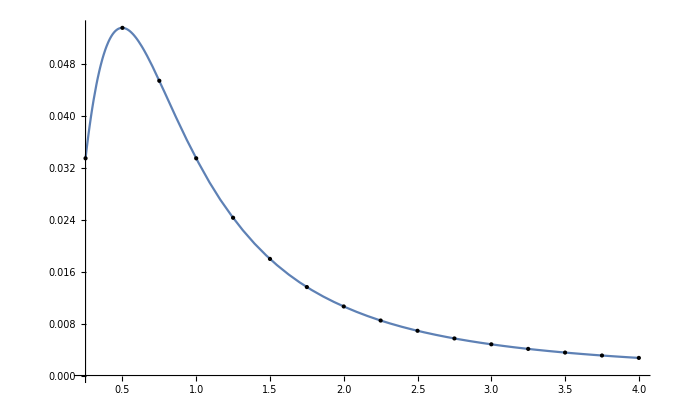

```mathematica
ListPlot[Transpose@{X,Y},PlotRange->{{1/4,4},{0,0.06}},PlotMarkers->{Automatic,5}];
f=Interpolation[Transpose@{X,Y},InterpolationOrder->5];
Plot[f[x],{x,1/4,4},Epilog->Point[Transpose@{X,Y}]]
(*Print["Min Value: (",InverseFunction[f][FindMinValue[{f[x],1/4<=x<=4},x]],",",FindMinValue[{f[x],1/4<=x<=4},x],")"];*)
```

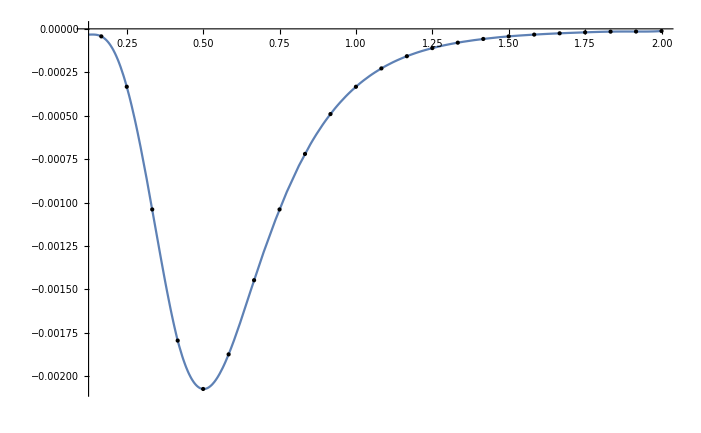

Min Value: (0.501745,-0.00207274)

```mathematica
ListPlot[Transpose@{X,Y},PlotRange->{{1/8,2},{-0.0022,0}},PlotMarkers->{Automatic,5}];
f=Interpolation[Transpose@{X,Y},InterpolationOrder->5];
Plot[f[x],{x,1/8,2},Epilog->Point[Transpose@{X,Y}]]
Print["Min Value: (",InverseFunction[f][FindMinValue[{f[x],1/8<=x<=2},x]],",",FindMinValue[{f[x],1/8<=x<=2},x],")"];
```

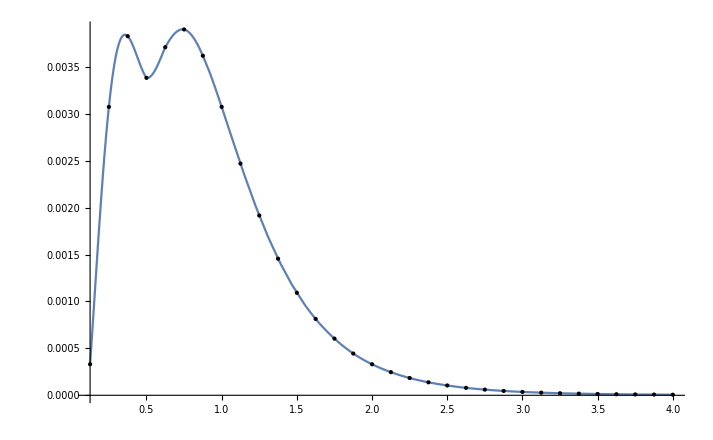

```mathematica
ListPlot[Transpose@{X,Y},PlotRange->{{1/8,4},{0,0.004}},PlotMarkers->{Automatic,5}];
f=Interpolation[Transpose@{X,Y},InterpolationOrder->5];
Plot[f[x],{x,1/8,4},Epilog->Point[Transpose@{X,Y}]]
(*Print["Min Value: (",InverseFunction[f][FindMinValue[{f[x],1/4<=x<=4},x]],",",FindMinValue[{f[x],1/4<=x<=4},x],")"];*)
```

```mathematica
NIntegrate[1/Subscript[τ, 2]^2,{Subscript[τ, 2],1,Infinity},{Subscript[τ, 1],-1/2,1/2}]+2*NIntegrate[1/Subscript[τ, 2]^2,{Subscript[τ, 2],(√3)/2,1},{Subscript[τ, 1],√(1-Subscript[τ, 2]^2),1/2}](*+NIntegrate[1/Subscript[τ, 2]^2,{Subscript[τ, 2],(√3)/2,1},{Subscript[τ, 1],-1/2,√(1-Subscript[τ, 2]^2)}]*)
```

1.0472

```mathematica
N[π/3]
```

1.0472

```mathematica
NIntegrate[1/Subscript[τ, 2]^2,{Subscript[τ, 2],(√3)/2,1},{Subscript[τ, 1],√(1-Subscript[τ, 2]^2),1/2}]
```

0.0235988

```mathematica
NIntegrate[1/Subscript[τ, 2]^2,{Subscript[τ, 2],(√3)/2,1},{Subscript[τ, 1],-1/2,-√(1-Subscript[τ, 2]^2)}]
```

0.0235988